```mathematica
muB = 6.71711388*10^(5);
p=0.6338;
V0 = 3.326;
xr = 9.9747;
cB = 1;
Bp=18.92*10^(-8);
hbar=7.63823302;
RLOffset=0.2;
```

```mathematica
V[x_]:=p*V0*(1-1/(1+(x/xr)^2))-cB*muB*Bp*x+RLOffset
```

```mathematica
NSolve[V[x]==0,x]
```

{{x→8.29355+5.54181 ⅈ},{x→8.29355-5.54181 ⅈ},{x→0.}}

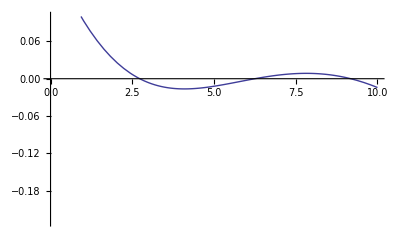

```mathematica
Plot[V[x],{x,0,10},PlotRange->{-0.23, 0.1}]
```

```mathematica
LH=Solve[V'[x]==0,x];xmin=x/.LH[[3]];Vmin=V[xmin];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Found=-0.0017058918;
```

```mathematica
DE=Found-Vmin;
```

```mathematica
AA=DE/(hbar*2*Pi)*10^6
```

305.743

```mathematica
1-AA/316.3
```

0.0333773